```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plot options for notebook

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

# A+B->C

Partition func matrix

```mathematica
fmatr[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{terms,nt,m,reps,vals,vecs,u,dm1,dm2,dl1,p,dl2,l1,l2,l3,l4,matr1,matr2}
,
terms={ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc};
nt=Length[terms];

reps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal,n->nVal};

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};

(* First derivatives of matrix *)
dm1=Association[];
Do[
dm1[i]=D[m,terms[[i]]]/.reps;
,{i,1,nt}];

(* Second derivatives *)
dm2=Association[];
Do[
Do[
dm2[{i,j}]=D[m,terms[[i]],terms[[j]]]/.reps;
,{j,i,nt}];
,{i,1,nt}];

(* Eigenvalues are in order high -> low *)
{{l1,l2,l3,l4},vecs}=Eigensystem[m/.reps];
u=Normalize/@vecs;

(* First derivative of largest eigenvalue *)
dl1=Association[];
p=Association[];
Do[
p[i]=Association[];
Do[
p[i][iu]=u[[1]].dm1[i].u[[iu]];
,{iu,1,4}];
dl1[i]=p[i][1];
,{i,1,nt}];

(* Second derivatives *)
dl2=Association[];
Do[
Do[
dl2[{i,j}]=u[[1]].dm2[{i,j}].u[[1]]+2*(
p[i][2]*p[j][2]/(l1-l2)
+p[i][3]*p[j][3]/(l1-l3)
+p[i][4]*p[j][4]/(l1-l4)
);
,{j,i,nt}];
,{i,1,nt}];

(* First derivative of n*Log(lambda) *)
matr1=ConstantArray[0,nt];
Do[
matr1[[i]]=nVal*dl1[i]/l1;
,{i,1,nt}];

(* Second derivative of n*Log(lambda) *)
matr2=ConstantArray[0,{nt,nt}];
Do[
Do[
matr2[[i,j]]=nVal*(dl2[{i,j}]-dl1[i]*dl1[j]/l1)/l1;
,{j,i,nt}];

(* Symmetric matrix *)
Do[
matr2[[i,j]]=matr2[[j,i]];
,{j,1,i-1}];
,{i,1,nt}];

Return[{matr1,matr2}]
];
```

### Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
fmatr[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps][[2]]
```

{{13.2509,0.654709,-5.41881,2.39466,16.792,2.05237,-1.50194,-4.66919,-1.23496},{0.654709,13.9696,-6.25737,-0.597468,8.86681,-2.70482,7.50692,1.34403,-1.72275},{-5.41881,-6.25737,13.0258,-0.704766,-10.2756,2.99021,-2.47146,8.26313,3.69236},{2.39466,-0.597468,-0.704766,1.86828,0.860152,0.0808607,-0.249351,-0.583969,-0.136387},{16.792,8.86681,-10.2756,0.860152,34.2432,-1.00259,-0.346799,-6.00812,-2.05495},{2.05237,-2.70482,2.99021,0.0808607,-1.00259,5.27467,-0.908129,0.117332,0.308893},{-1.50194,7.50692,-2.47146,-0.249351,-0.346799,-0.908129,8.53117,-0.678817,-0.514561},{-4.66919,1.34403,8.26313,-0.583969,-6.00812,0.117332,-0.678817,14.3306,0.87338},{-1.23496,-1.72275,3.69236,-0.136387,-2.05495,0.308893,-0.514561,0.87338,2.69994}}

### Check

```mathematica
m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};
```

```mathematica
(* largest eigenvalue*)
```

```mathematica
lp=Eigenvalues[m,Quartics->True][[-1]];
```

```mathematica
(* First component of the matrix *)
```

```mathematica
D[n*Log[lp],{ha,2}]/.reps
```

13.2509-3.6986×10^-16 ⅈ

Triplet moment

```mathematica
ftriplet[x_,y_,z_,haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{rdx,rdz,rhx,rhy,rhz,rjxy,rjyz,hjreps,
vals,vecs,u,reps,ureps,lreps,aveSimpz,m},
If[x=="A",rdx={dxa->1,dxb->0,dxc->0};rhx={hx->haVal};];
If[x=="B",rdx={dxa->0,dxb->1,dxc->0};rhx={hx->hbVal};];
If[x=="C",rdx={dxa->0,dxb->0,dxc->1};rhx={hx->hcVal};];
If[z=="A",rdz={dza->1,dzb->0,dzc->0};rhz={hz->haVal};];
If[z=="B",rdz={dza->0,dzb->1,dzc->0};rhz={hz->hbVal};];
If[z=="C",rdz={dza->0,dzb->0,dzc->1};rhz={hz->hcVal};];
If[y=="A",rhy={hy->haVal};];
If[y=="B",rhy={hy->hbVal};];
If[y=="C",rhy={hy->hcVal};];
If[x=="A"&&y=="A",rjxy={jxy->jaaVal}];
If[(x=="A"&&y=="B")||(x=="B"&&y=="A"),rjxy={jxy->jabVal}];
If[(x=="A"&&y=="C")||(x=="C"&&y=="A"),rjxy={jxy->jacVal}];
If[x=="B"&&y=="B",rjxy={jxy->jbbVal}];
If[(x=="B"&&y=="C")||(x=="C"&&y=="B"),rjxy={jxy->jbcVal}];
If[x=="C"&&y=="C",rjxy={jxy->jccVal}];
If[y=="A"&&z=="A",rjyz={jyz->jaaVal}];
If[(y=="A"&&z=="B")||(y=="B"&&z=="A"),rjyz={jyz->jabVal}];
If[(y=="A"&&z=="C")||(y=="C"&&z=="A"),rjyz={jyz->jacVal}];
If[y=="B"&&z=="B",rjyz={jyz->jbbVal}];
If[(y=="B"&&z=="C")||(y=="C"&&z=="B"),rjyz={jyz->jbcVal}];
If[y=="C"&&z=="C",rjyz={jyz->jccVal}];

hjreps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal};

reps=Join[rdx,rdz,rhx,rhy,rhz,rjxy,rjyz,{n->nVal},hjreps];

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
}/.reps;

{vals,vecs}=Eigensystem[m];
u=Normalize/@vecs;

ureps=Flatten[Table[ToExpression["u"<>ToString[i]<>ToString[j]]->u[[i,j]],{i,1,4},{j,1,4}],1];
lreps=Table[ToExpression["l"<>ToString[i]]->vals[[i]],{i,1,4}];

reps=Join[reps,ureps,lreps];

aveSimpz=(ⅇ^(hx/2+hy+hz/2+jxy+jyz) l1^(-3+n) n (dxa u12+dxb u13+dxc u14) (dza u12+dzb u13+dzc u14) (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)^2)/(l1^(-1+n) u11 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u21 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u31 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u41 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)+ⅇ^(ha/2) (l1^(-1+n) u12 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u22 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u32 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u42 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hb/2) (l1^(-1+n) u13 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u23 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u33 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u43 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hc/2) (l1^(-1+n) u14 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u24 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u34 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u44 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)));

Return[aveSimpz/.reps]
];
```

Time derivatives of the moments

```mathematica
fdmoments[kf_,matr1_,trip_]:=Module[
{der}
,
(* 
Order of matrix in derivatives of log(Z)=n*log(lambda)
ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc
Recall that jab controls the sum of both moments: < a(i) b(i+1) > + < b(i) a(i+1) > 
*)

(* Order of derivatives: same *)

(* Order of triplet moments:
aab, aba, baa, abb, bab, bba, abc, bac, cab, cba
*)

der=ConstantArray[0,9];
der[[1]]=-kf*matr1[[5]];
der[[2]]=-kf*matr1[[5]];
der[[3]]=kf*matr1[[5]];
der[[4]]=-kf*trip[[1]];
der[[5]]=-kf*matr1[[5]]-kf*trip[[2]]-kf*trip[[5]];
der[[6]]=0.5*kf*trip[[1]]+kf*trip[[2]]-kf*trip[[9]]+0.5*kf*trip[[3]];
der[[7]]=-kf*trip[[6]];
der[[8]]=kf*trip[[5]]+0.5*kf*trip[[6]]+0.5*kf*trip[[4]]-kf*trip[[10]];
der[[9]]=0.5*kf*trip[[7]]+0.5*kf*trip[[9]]+0.5*kf*trip[[8]]+0.5*kf*trip[[10]];

Return[der];
];
```

Get basis functions

```mathematica
bfs[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_,kf_]:=Module[
{matr1,matr2,ts,trip,dmoments,bs}
,

(* Get the matrices *)
{matr1,matr2}=fmatr[haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];

(* Get the triplet moments *)
ts={{"A","A","B"},{"A","B","A"},{"B","A","A"},{"A","B","B"},{"B","A","B"},{"B","B","A"},{"A","B","C"},{"B","A","C"},{"C","A","B"},{"C","B","A"}};
trip=ConstantArray[0,10];
Do[
trip[[i]]=ftriplet[ts[[i,1]],ts[[i,2]],ts[[i,3]],haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];
,{i,1,10}];

(* Get the time derivatives of the moments *)
dmoments=fdmoments[kf,matr1,trip];

(* Solve for the basis functions *)
bs=Inverse[matr2].dmoments;

Return[bs]
];
```

Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
kf=1.0;
```

```mathematica
bfs[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps,kf]
```

{-5.16231,-6.39472,-2.50547,3.30953,3.08603,2.11179,4.86252,2.51799,0.583192}

# Plots

Default values

```mathematica
haDef=0.0;
hbDef=0.0;
hcDef=0.0;
jaaDef=0.0;
jabDef=0.0;
jacDef=0.0;
jbbDef=0.0;
jbcDef=0.0;
jccDef=0.0;
nDef=1000.0;
kfDef=1.0;
```

## F_{h_A}

All 9 dimensions

```mathematica
rngmin=-2.0;
rngmax=2.0;
drng=0.4;
pltDataHA=Association[];
Do[
Do[
Print[{i,j}];
pltDataHA[{i,j}]=Flatten[Table[{vary1,vary2,bfs[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef,kfDef][[1]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{1,8}

{1,9}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{2,8}

{2,9}

{3,4}

{3,5}

{3,6}

{3,7}

{3,8}

{3,9}

{4,5}

{4,6}

{4,7}

{4,8}

{4,9}

{5,6}

{5,7}

{5,8}

{5,9}

{6,7}

{6,8}

{6,9}

{7,8}

{7,9}

{8,9}

```mathematica
pltMomHA=Association[];
Do[
Do[
Print[{j,i}];
pltMomHA[{j,i}]=Flatten[Table[{vary1,vary2,fmatr[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef][[1,1]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{2,1}

{3,1}

{4,1}

{5,1}

{6,1}

{7,1}

{8,1}

{9,1}

{3,2}

{4,2}

{5,2}

{6,2}

{7,2}

{8,2}

{9,2}

{4,3}

{5,3}

{6,3}

{7,3}

{8,3}

{9,3}

{5,4}

{6,4}

{7,4}

{8,4}

{9,4}

{6,5}

{7,5}

{8,5}

{9,5}

{7,6}

{8,6}

{9,6}

{8,7}

{9,7}

{9,8}

```mathematica
pltRng={-20,0};
pltTbl=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomHA[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataHA[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,1,9}
,{j,1,9}];
```

```mathematica
GraphicsGrid[pltTbl,ImageSize->1000]
```

-Graphics-

Smaller grid, as func of ha,hb,jab

```mathematica
pltRng={-20,0};
pltTblS=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomHA[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataHA[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,{1,2,5}}
,{j,{1,2,5}}];
```

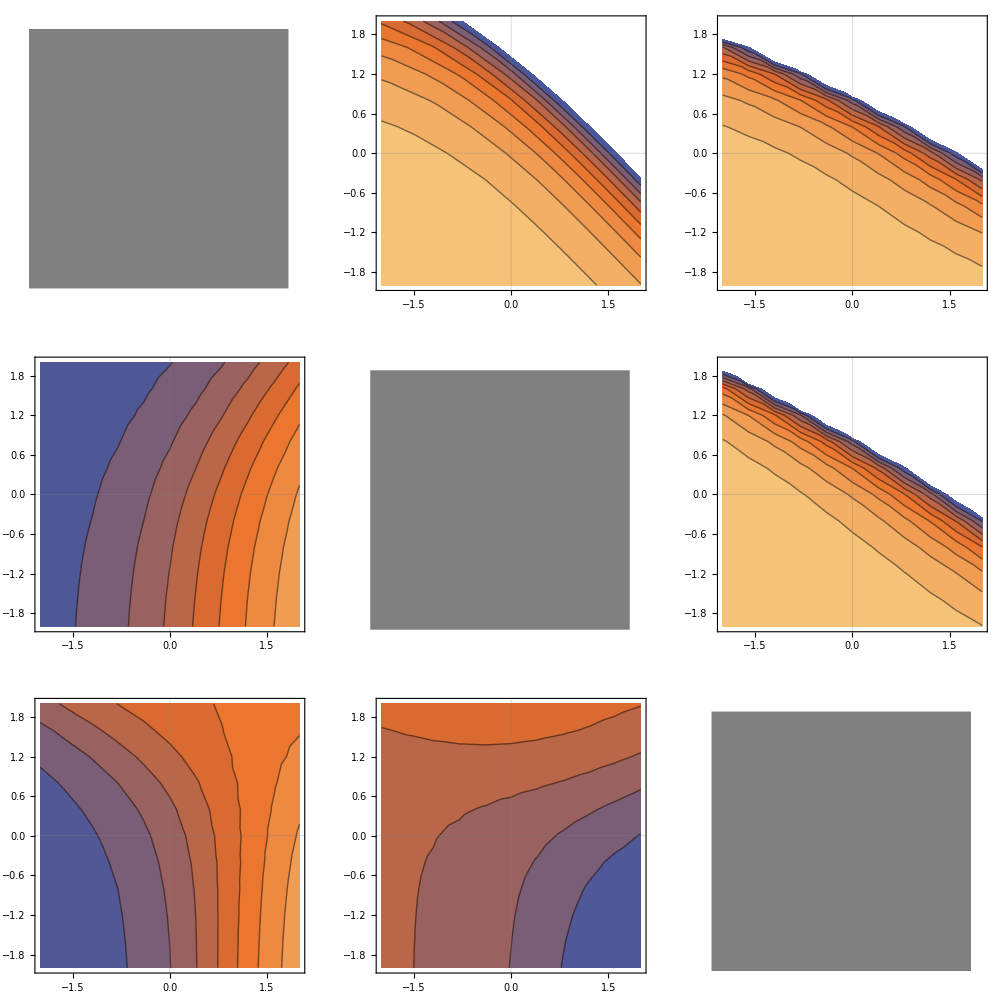

```mathematica
pltHAS=GraphicsGrid[pltTblS,ImageSize->1000]
```

```mathematica
Export["../figures_bfs_trivalent_forward/ha.pdf",pltHAS];
```

../figures_trivalent_forward/ha.pdf

Export individual plots

```mathematica
pltRngi={-10,10};
pltTblSi=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomHA[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataHA[{i,j}],ColorFunction->ColorData[{colorFunc,pltRngi}],ColorFunctionScaling->False,PlotRange->pltRngi,ImagePadding->1]
]
]
,{i,{1,2,5}}
,{j,{1,2,5}}];
```

```mathematica
Export["../figures_bfs_trivalent_forward/ha/ha_hb.png",pltTblSi[[1,2]]]
```

../figures_trivalent_forward/ha/ha_hb.png

```mathematica
Export["../figures_bfs_trivalent_forward/ha/ha_hb_moment.png",pltTblSi[[2,1]]]
```

../figures_trivalent_forward/ha/ha_hb_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/ha/ha_jab.png",pltTblSi[[1,3]]]
```

../figures_trivalent_forward/ha/ha_jab.png

```mathematica
Export["../figures_bfs_trivalent_forward/ha/ha_jab_moment.png",pltTblSi[[3,1]]]
```

../figures_trivalent_forward/ha/ha_jab_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/ha/hb_jab.png",pltTblSi[[2,3]]]
```

../figures_trivalent_forward/ha/hb_jab.png

```mathematica
Export["../figures_bfs_trivalent_forward/ha/hb_jab_moment.png",pltTblSi[[3,2]]]
```

../figures_trivalent_forward/ha/hb_jab_moment.png

```mathematica
leg1=BarLegend[{colorFunc,pltRngi},LabelStyle->{FontSize->30}]
```

```mathematica
Export["../figures_bfs_trivalent_forward/leg1.png",leg1]
```

../figures_trivalent_forward/leg1.png

```mathematica
leg2=BarLegend[{colorFunc,{0,nDef}},LabelStyle->{FontSize->30}]
```

```mathematica
Export["../figures_bfs_trivalent_forward/leg2.png",leg2]
```

../figures_trivalent_forward/leg2.png

## F_{J_{AB}}

Plot 9 dimensional gird

```mathematica
rngmin=-2.0;
rngmax=2.0;
drng=0.4;
pltDataJAB=Association[];
Do[
Do[
Print[{i,j}];
pltDataJAB[{i,j}]=Flatten[Table[{vary1,vary2,bfs[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef,kfDef][[5]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{1,8}

{1,9}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{2,8}

{2,9}

{3,4}

{3,5}

{3,6}

{3,7}

{3,8}

{3,9}

{4,5}

{4,6}

{4,7}

{4,8}

{4,9}

{5,6}

{5,7}

{5,8}

{5,9}

{6,7}

{6,8}

{6,9}

{7,8}

{7,9}

{8,9}

```mathematica
pltMomJAB=Association[];
Do[
Do[
Print[{j,i}];
pltMomJAB[{j,i}]=Flatten[Table[{vary1,vary2,fmatr[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef][[1,5]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{2,1}

{3,1}

{4,1}

{5,1}

{6,1}

{7,1}

{8,1}

{9,1}

{3,2}

{4,2}

{5,2}

{6,2}

{7,2}

{8,2}

{9,2}

{4,3}

{5,3}

{6,3}

{7,3}

{8,3}

{9,3}

{5,4}

{6,4}

{7,4}

{8,4}

{9,4}

{6,5}

{7,5}

{8,5}

{9,5}

{7,6}

{8,6}

{9,6}

{8,7}

{9,7}

{9,8}

```mathematica
pltRng={0,10};
pltTblJAB=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAB[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataJAB[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,1,9}
,{j,1,9}];
```

```mathematica
GraphicsGrid[pltTblJAB,ImageSize->1000]
```

-Graphics-

Smaller grid, as func of ha, hb, jab

```mathematica
pltRng={0,10};
pltTblJABS=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAB[{i,j}],ColorFunction->ColorData[{colorFunc,{0,400.0}}],ColorFunctionScaling->False,PlotRange->{0,400.0},ImagePadding->1],
ListContourPlot[pltDataJAB[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,{1,2,5}}
,{j,{1,2,5}}];
```

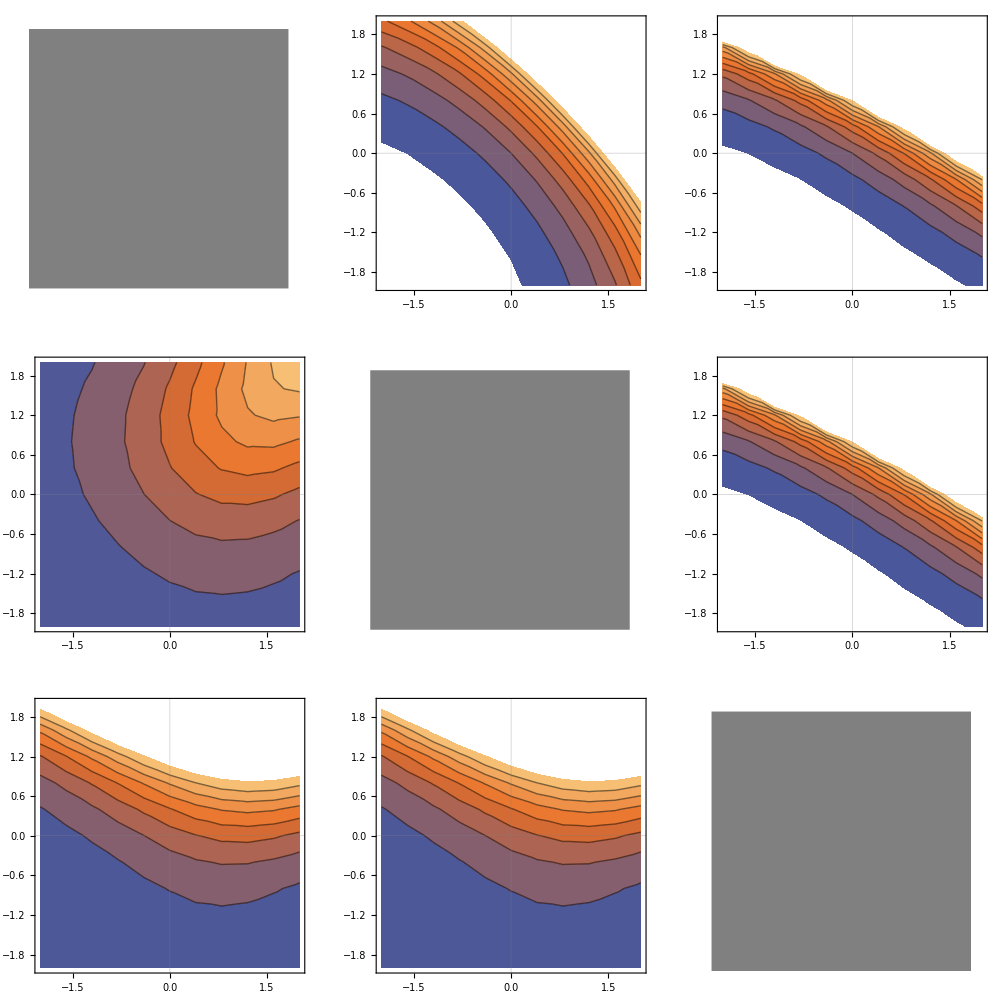

```mathematica
pltJABS=GraphicsGrid[pltTblJABS,ImageSize->1000]
```

```mathematica
Export["../figures_bfs_trivalent_forward/jab.pdf",pltJABS]
```

../figures_trivalent_forward/jab.pdf

Make individual plots

```mathematica
pltRngi={-10,10};
pltTblJABSi=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAB[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataJAB[{i,j}],ColorFunction->ColorData[{colorFunc,pltRngi}],ColorFunctionScaling->False,PlotRange->pltRngi,ImagePadding->1]
]
]
,{i,{1,2,5}}
,{j,{1,2,5}}];
```

```mathematica
Export["../figures_bfs_trivalent_forward/jab/ha_hb.png",pltTblJABSi[[1,2]]]
```

../figures_trivalent_forward/jab/ha_hb.png

```mathematica
Export["../figures_bfs_trivalent_forward/jab/ha_hb_moment.png",pltTblJABSi[[2,1]]]
```

../figures_trivalent_forward/jab/ha_hb_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/jab/ha_jab.png",pltTblJABSi[[1,3]]]
```

../figures_trivalent_forward/jab/ha_jab.png

```mathematica
Export["../figures_bfs_trivalent_forward/jab/ha_jab_moment.png",pltTblJABSi[[3,1]]]
```

../figures_trivalent_forward/jab/ha_jab_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/jab/hb_jab.png",pltTblJABSi[[2,3]]]
```

../figures_trivalent_forward/jab/hb_jab.png

```mathematica
Export["../figures_bfs_trivalent_forward/jab/hb_jab_moment.png",pltTblJABSi[[3,2]]]
```

../figures_trivalent_forward/jab/hb_jab_moment.png

## F_{J_{AC}}

Plot 9 dimensional grid

```mathematica
rngmin=-2.0;
rngmax=2.0;
drng=0.4;
pltDataJAC=Association[];
Do[
Do[
Print[{i,j}];
pltDataJAC[{i,j}]=Flatten[Table[{vary1,vary2,bfs[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef,kfDef][[6]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{1,8}

{1,9}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{2,8}

{2,9}

{3,4}

{3,5}

{3,6}

{3,7}

{3,8}

{3,9}

{4,5}

{4,6}

{4,7}

{4,8}

{4,9}

{5,6}

{5,7}

{5,8}

{5,9}

{6,7}

{6,8}

{6,9}

{7,8}

{7,9}

{8,9}

```mathematica
pltMomJAC=Association[];
Do[
Do[
Print[{j,i}];
pltMomJAC[{j,i}]=Flatten[Table[{vary1,vary2,fmatr[
If[i==1,vary1,If[j==1,vary2,haDef]],
If[i==2,vary1,If[j==2,vary2,hbDef]],
If[i==3,vary1,If[j==3,vary2,hcDef]],
If[i==4,vary1,If[j==4,vary2,jaaDef]],
If[i==5,vary1,If[j==5,vary2,jabDef]],
If[i==6,vary1,If[j==6,vary2,jacDef]],
If[i==7,vary1,If[j==7,vary2,jbbDef]],
If[i==8,vary1,If[j==8,vary2,jbcDef]],
If[i==9,vary1,If[j==9,vary2,jccDef]],
nDef][[1,6]]},
{vary1,rngmin,rngmax,drng},
{vary2,rngmin,rngmax,drng}],1];
,{j,i+1,9}];
,{i,1,9}];
```

{2,1}

{3,1}

{4,1}

{5,1}

{6,1}

{7,1}

{8,1}

{9,1}

{3,2}

{4,2}

{5,2}

{6,2}

{7,2}

{8,2}

{9,2}

{4,3}

{5,3}

{6,3}

{7,3}

{8,3}

{9,3}

{5,4}

{6,4}

{7,4}

{8,4}

{9,4}

{6,5}

{7,5}

{8,5}

{9,5}

{7,6}

{8,6}

{9,6}

{8,7}

{9,7}

{9,8}

```mathematica
pltRng={0,10};
pltTblJAC=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAC[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataJAC[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,1,9}
,{j,1,9}];
```

```mathematica
GraphicsGrid[pltTblJAC,ImageSize->1000]
```

-Graphics-

Smaller grid, as func of ha, hc, jac

```mathematica
pltRng={0,10};
pltTblJACS=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAC[{i,j}],ColorFunction->ColorData[{colorFunc,{0,200.0}}],ColorFunctionScaling->False,PlotRange->{0,200.0},ImagePadding->1],
ListContourPlot[pltDataJAC[{i,j}],ColorFunction->ColorData[{colorFunc,pltRng}],ColorFunctionScaling->False,PlotRange->pltRng,ImagePadding->1]
]
]
,{i,{1,3,6}}
,{j,{1,3,6}}];
```

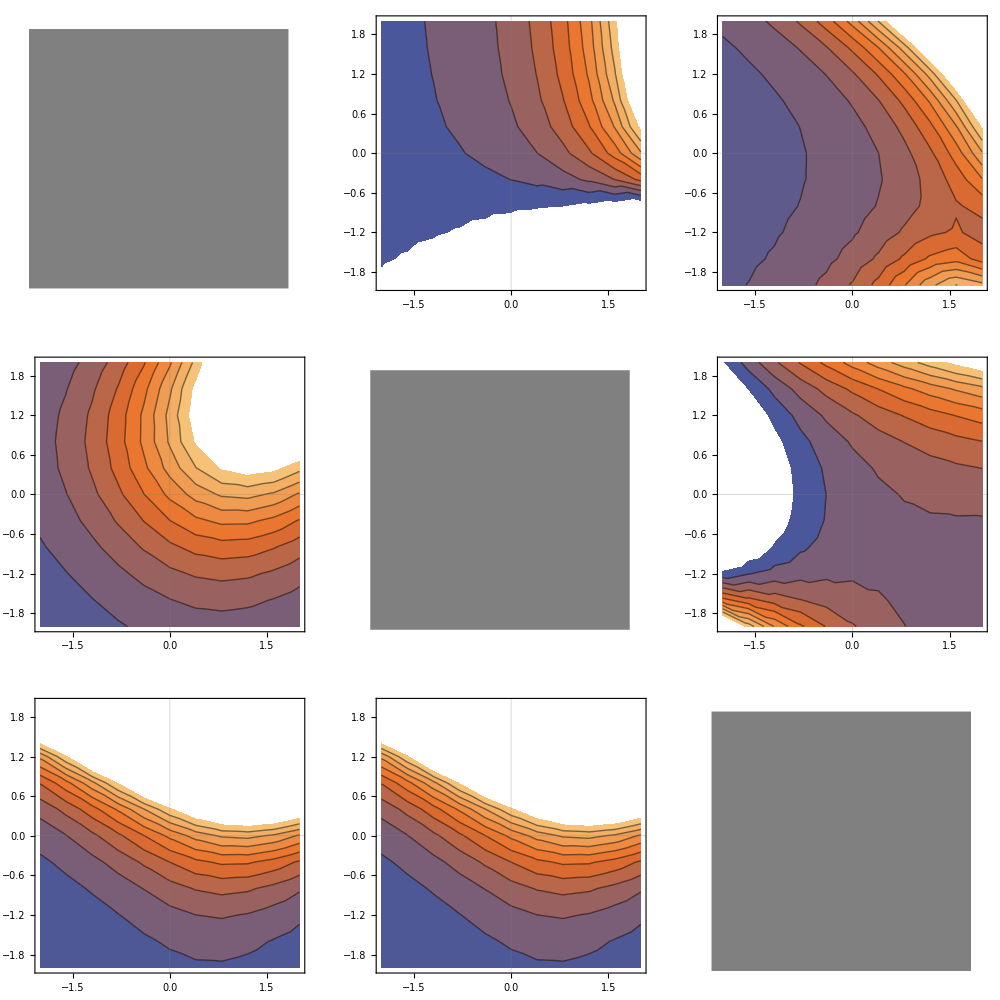

```mathematica
pltJACS=GraphicsGrid[pltTblJACS,ImageSize->1000]
```

```mathematica
Export["../figures_bfs_trivalent_forward/jac.pdf",pltJACS]
```

../figures_trivalent_forward/jac.pdf

Make individual plots

```mathematica
pltRngi={-10,10};
pltTblJACSi=Table[
If[i==j,
Graphics[{Gray,Rectangle[]}],
If[i>j,
ListContourPlot[pltMomJAC[{i,j}],ColorFunction->ColorData[{colorFunc,{0,nDef}}],ColorFunctionScaling->False,PlotRange->{0,nDef},ImagePadding->1],
ListContourPlot[pltDataJAC[{i,j}],ColorFunction->ColorData[{colorFunc,pltRngi}],ColorFunctionScaling->False,PlotRange->pltRngi,ImagePadding->1]
]
]
,{i,{1,2,5}}
,{j,{1,2,5}}];
```

```mathematica
Export["../figures_bfs_trivalent_forward/jac/ha_hc.png",pltTblJACSi[[1,2]]]
```

../figures_trivalent_forward/jac/ha_hc.png

```mathematica
Export["../figures_bfs_trivalent_forward/jac/ha_hc_moment.png",pltTblJACSi[[2,1]]]
```

../figures_trivalent_forward/jac/ha_hc_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/jac/ha_jac.png",pltTblJACSi[[1,3]]]
```

../figures_trivalent_forward/jac/ha_jac.png

```mathematica
Export["../figures_bfs_trivalent_forward/jac/ha_jac_moment.png",pltTblJACSi[[3,1]]]
```

../figures_trivalent_forward/jac/ha_jac_moment.png

```mathematica
Export["../figures_bfs_trivalent_forward/jac/hc_jac.png",pltTblJACSi[[2,3]]]
```

../figures_trivalent_forward/jac/hc_jac.png

```mathematica
Export["../figures_bfs_trivalent_forward/jac/hc_jac_moment.png",pltTblJACSi[[3,2]]]
```

../figures_trivalent_forward/jac/hc_jac_moment.png